## tFunctions

```mathematica
CaesarCipher[plaintext_, key_]:= FromCharacterCode[ Mod[ ToCharacterCode[plaintext] - 97 +key, 26] + 97]
```

```mathematica
RotI={1->5,2->11,3->13,4->6,5->12,6->7,7->4,8->17,9->22,10->26,11->14,12->20,13->15,14->23,15->25,16->8,17->24,18->21,19->19,20->16,21->1,22->9,23->2,24->18,25->3,26->10}
```

{1→5,2→11,3→13,4→6,5→12,6→7,7→4,8→17,9→22,10→26,11→14,12→20,13→15,14→23,15→25,16→8,17→24,18→21,19→19,20→16,21→1,22→9,23→2,24→18,25→3,26→10}

```mathematica
RotIinv={5->1,11->2,13->3,6->4,12->5,7->6,4->7,17->8,22->9,26->10,14->11,20->12,15->13,23->14,25->15,8->16,24->17,21->18,19->19,16->20,1->21,9->22,2->23,18->24,3->25,10->26}
```

{5→1,11→2,13→3,6→4,12→5,7→6,4→7,17→8,22→9,26→10,14→11,20→12,15→13,23→14,25→15,8→16,24→17,21→18,19→19,16→20,1→21,9→22,2→23,18→24,3→25,10→26}

```mathematica
RefB={1->25,25->1,2->18, 18->2,3->21, 21->3,4->8, 8->4, 5->17, 17->5, 6->19, 19->6,7->12, 12->7, 9->16, 16->9, 10->24, 24->10, 11->14, 14 ->11,13->15,15->13,20->26,26->20,22->23,23->22}
```

{1→25,25→1,2→18,18→2,3→21,21→3,4→8,8→4,5→17,17→5,6→19,19→6,7→12,12→7,9→16,16→9,10→24,24→10,11→14,14→11,13→15,15→13,20→26,26→20,22→23,23→22}

```mathematica
EnigmaGuts = {1->8,2->11,3->13,4->19,5->6,6->5,7->16,8->1,9->14,10->12,11->2,12->10,13->3,14->9,15->21,16->7,17->26,18->25,19->4,20->22,21->15,22->20,23->24,24->23,25->18,26->17}
```

{1→8,2→11,3→13,4→19,5→6,6→5,7→16,8→1,9→14,10→12,11→2,12→10,13→3,14→9,15→21,16→7,17→26,18→25,19→4,20→22,21→15,22→20,23→24,24→23,25→18,26→17}

```mathematica
Enigma1[x_,n_]:=Mod[((Replace[Mod[x+n,26,1],EnigmaGuts])-n),26,1]
```

## tTest1

```mathematica
ptt1= "iamwhoiam";
kt1 = 21 ;
ctt1 = CaesarCipher[ptt1,kt1];
ctt1
```

dvhrcjdvh

```mathematica
CaesarCipher["iamwhoiam",21]
```

dvhrcjdvh

```mathematica
"dvhrcjdvh"
```

dvhrcjdvh

```mathematica
Manipulate[CaesarCipher[ctt1,n],{n,1,26,1}]
```

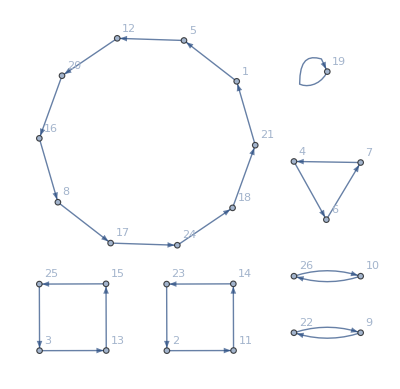

```mathematica
Graph[RotI,VertexLabels->"Name"]
```

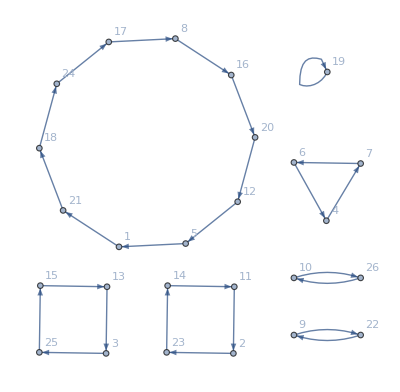

```mathematica
Graph[RotIinv,VertexLabels->"Name"]
```

```mathematica
lettercodes=Range[26]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26}

```mathematica
ReplaceAll[ReplaceAll[lettercodes,RotI],RotIinv]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26}

```mathematica
ReplaceAll[lettercodes,RotI]
```

{5,11,13,6,12,7,4,17,22,26,14,20,15,23,25,8,24,21,19,16,1,9,2,18,3,10}

```mathematica
ReplaceAll[ReplaceAll[lettercodes,RefB],RefB]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26}

```mathematica
Table[ReplaceAll[ReplaceAll[ReplaceAll[x,RotI],RefB],RotIinv],{x,1,26,1}]
```

{8,11,13,19,6,5,16,1,14,12,2,10,3,9,21,7,26,25,4,22,15,20,24,23,18,17}

```mathematica
Table[ReplaceAll[x,EnigmaGuts],{x,1,26,1}]
```

{8,11,13,19,6,5,16,1,14,12,2,10,3,9,21,7,26,25,4,22,15,20,24,23,18,17}

```mathematica
Table[Enigma1[1,n],{n,0,25,1}]
```

{8,10,11,16,2,26,10,20,6,3,18,25,17,22,7,18,10,8,12,3,21,25,2,26,20,18}

```mathematica
list1 = Table[Enigma1[1,n],{n,0,25,1}]
```

{8,10,11,16,2,26,10,20,6,3,18,25,17,22,7,18,10,8,12,3,21,25,2,26,20,18}

```mathematica
MapThread[Enigma1,{list1,{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
EnigmaMachine[text_,key_] := MapThread[Enigma1,{text,Table[Mod[(key+n),26,0],{n,0,Length[text]-1,1}]}]
```

```mathematica
EnigmaMachine[{1,2,3,4,5},2]
```

{11,3,12,9,22}

```mathematica
EnigmaMachine[EnigmaMachine[{1,2,3,4,5},2],2]
```

{1,2,3,4,5}